# Evaluating freewill in the computationally reducible pockets of a computationally irreducible world -Graphics-

Abstract
“free will is the supposed power or capacity of humans to make decisions or perform actions independently of any prior event or state of the universe.”.In this computational essay, we use Neural Networks to explore free will by exploring how weight trajectories while training  neural networks, converge or diverge and treat weight trajectories as computational proxies to free will. We also draw upon the concepts of computational irreducibility to explore if the weights of Artificial neural networks are computationally reducible or not.


Introduction

Would we say that an ant has any degree of freedom or gets to exercise its freedom of will if we can reasonably predict its actions?Probably not.What about humans?Can we predict what a human agent is going to do before the agent carries out their actions with great certainty?Probably not.

“While many computations admit shortcuts that allow them to be performed more rapidly,others cannot be sped up.Computations that cannot be sped up by means of any shortcut are called computationally irreducible.The principle of computational irreducibility says that the only way to determine the answer to a computationally irreducible question is to perform,or simulate,the computation.Some irreducible computations can be sped up by performing them on faster hardware,as the principle refers only to computation time.”

We posit that a system that has "free will" ,will exhibit lots of different behaviors and one that does not will exhibit very few.We are interested in when neural nets,an emulation of biological thinking processes,exhibit free will.We base our experiment on Dr.Wolfram's Article "What's Really Going On in Machine Learning" where he sets up mesh neural networks to predict cellular automata and observes how different random weights affects his results.We start by choosing a mathematical function that our neural networks shall model.

## Methodology

For this experiment, we wanted to choose a simple mathematical function to model and picked the  piecewise function below

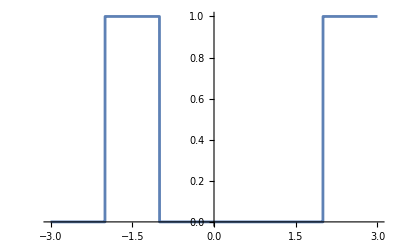

```mathematica
whichFunction[x_] := Which[
      x < -2, 0,
      -2 < x < -1, 1,
      -1 < x < 2, 0,
      x > 2, 1,
      True, 0  
    ]
  
Plot[whichFunction[x], {x, -3, 3}, PlotRange -> {0, 1}]
```

## 1)We first decided on a stopping percent (10,20,30,40,50,60,70,80,90%), and a “simple” neural net architecture, e.g., a small number of LinearLayer with a small number of neurons 2)We then initialized the net with random weights(Randomizing the seed as well) 3)We trained 2 identical neural nets to recreate the function and recorded the number of rounds/epochs - We then stored the weights (and the final loss) in a list 4)We reset the weights via NetInitialize 5)Retrained the 2 neural networks for 10,20,30,40,50,60,70,80 and 90 percent of the rounds we know would lead to convergence 6)recorded the net loss which we assume to be higher than our threshold) and weights 7)Calculated the distance between the weights of the neural networks layer wise 8)Plotted our results

We start by generating  our training data below by looping through the  piecewise function from a range of -3 to +3

```mathematica
trainingDataFormatted=Table[{x}->{N[whichFunction[x]]},{x,-3,3,0.001}];
```

## Architecture of the neural network

Our neural networks with 3 layers have been set up below with 5 neurons in each layer.
These specific model configurations were chosen through trial and error while keeping simplicity in mind.We have chosen ReLU(Ramp) as our activation function while keeping the standard Mean squared error as our loss function. We have also chosen the Adam Optimiser to avoid getting stuck in local minima/maxima
-Graphics-

```mathematica
newNet[]:=NetChain[
  {
    LinearLayer[5,"Input"->1],
    ElementwiseLayer[Ramp],
    LinearLayer[5,"Input"->5],
    ElementwiseLayer[Ramp],
    LinearLayer[1,"Input"->5]
  }
]

listOfNetworks=Table[newNet[],{2}]
```

{NetChain[…],NetChain[…]}

Initialized the neural network with random weights.

```mathematica
initialiseNetworks[i_]:=Module[
  {netInitialized},
  netInitialized=NetInitialize[listOfNetworks[[i]],Method->{"Random"},RandomSeeding->Automatic];
  netInitialized
]

netxInitialized=Table[initialiseNetworks[i],{i,2}]
```

{NetChain[…],NetChain[…]}

Trained the model while checkpointing the weights in a local directory. We implemented early stopping to get a more accurate estimate of the number of rounds required for our neural network to reach convergence. If there wasn’t a 0.001 change in the Mean squared error over the last 40 epochs then the neural network would stop training.

checkpointold

NetTrain::novalidation: No validation set provided, defaulting to training set for stopping criterion.

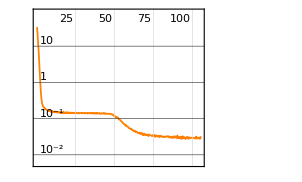
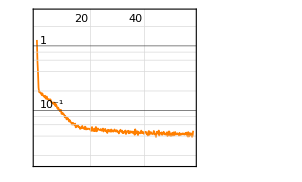
{NetTrainResultsObject[NetTrain Results
summary | ,,  batches:9870  rounds:105  time:15s  examples/s:44741
data | ,,  training examples:6001  processed examples:631680  skipped examples:0
method | ,,  ADAMoptimizer  batch size64CPU
round | ,,  loss:2.87×10^-2
 | rounds
loss | -Graphics- | 
 | ],NetTrainResultsObject[NetTrain Results
summary | ,,  batches:5452  rounds:58  time:7.5s  examples/s:46768
data | ,,  training examples:6001  processed examples:348928  skipped examples:0
method | ,,  ADAMoptimizer  batch size64CPU
round | ,,  loss:4.26×10^-2
 | rounds
loss | -Graphics- | 
 | ]}

```mathematica
checkpointDir="checkpointold"
netxtrained[x_]:=Module[
    {trainedNetPiece},
    trainedNetPiece=NetTrain[
        netxInitialized[[x]],
        trainingDataFormatted,All,
        TrainingStoppingCriterion-><|"Criterion"->"Loss","Patience"->40,"AbsoluteChange"->0.001|>,
        TrainingProgressCheckpointing->{"Directory",checkpointDir,"Interval"->Quantity[1,"Rounds"]}
    ];
    trainedNetPiece
]

listoftrained=Table[netxtrained[i],{i,2}]
```

We can retrieve the number of "rounds" the model took to reach convergence

```mathematica
convergencetime1 = listoftrained[[1]]["TotalRounds"]
convergencetime2=listoftrained[[2]]["TotalRounds"]
```

105

C:\Users\agast\checkpointsNetNew909

NetTrain::novalidation: No validation set provided, defaulting to training set for stopping criterion.

NetChain[…]

We then extract the weights of our 2 neural networks  by looping through each layer of the neural network with Table and then extracting the weights with NetExtract

```mathematica
listofweights=Table[
    Table[
        Normal[NetExtract[listoftrained[[i]]["TrainedNet"],{j,"Weights"}]],
        {j,1,Length[netxInitialized[[i]]],2}
    ],
    {i,Length[listoftrained]}
]
```

{{{{0.964514},{-0.997123},{1.98036},{2.1336},{2.14097}},{{1.94281,0.286229,0.0261989,-0.717161,-0.621413},{0.859143,0.34558,1.11493,1.05162,1.95679},{2.14984,-1.20094,-1.29286,-0.507824,-0.19466},{0.623067,0.0534587,0.27753,-0.120711,1.19996},{-0.266109,-0.295021,0.334102,-0.0736108,-0.0928823}},{{-2.75539,-0.445644,1.2093,1.16474,-0.648559}}},{{{-0.347638},{0.610167},{-1.64122},{-1.43561},{-1.72367}},{{0.308517,1.07235,-0.635279,-0.249436,1.92139},{-2.41844,0.225225,0.102384,-1.84304,0.495108},{-2.32576,1.32079,-0.39609,-0.485773,-0.203174},{1.48532,-1.45058,1.98359,-0.321209,-0.858037},{1.2533,0.318556,-0.511484,0.0525916,1.10971}},{{0.853474,-1.17729,0.823206,-0.649612,-0.860967}}}}

To calculate the distance between the weights of our neural networks, we must first sort the weights of each layer in ascending order. This is because neurons in an artificial neural network may be permutations of each other. We then Map the corresponding weights and calculate the euclidean distance between them

```mathematica
orderedWeights1 = Table[Sort[listofweights[[1]][[i]]], {i, 1, Length[listofweights[[1]]], 1}];
orderedWeights2 = Table[Sort[listofweights[[2]][[i]]], {i, 1, Length[listofweights[[2]]], 1}];
```

```mathematica
euclideanDistances=MapThread[EuclideanDistance,{orderedWeights1,orderedWeights2}];
totalDistance=Total[euclideanDistances];

totalDistance
```

11.7557

We can now plot the output of our trained neural nets against the objective function

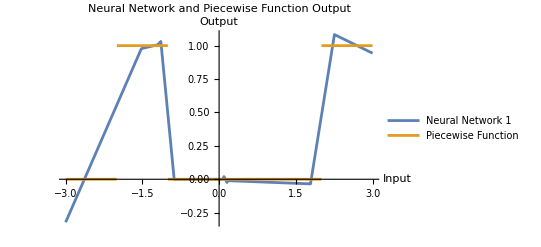

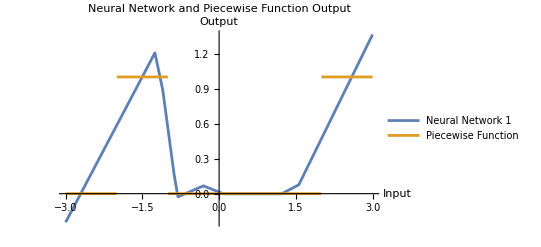

```mathematica
Plot[
    {
        listoftrained[[1]]["TrainedNet"][x] // Normal,
   
        whichFunction[x]
    },
    {x,-3,3},
    PlotRange->All,
    PlotLabel->"Neural Network and Piecewise Function Output",
    AxesLabel->{"Input","Output"},
    PlotLegends->{"Neural Network 1","Piecewise Function"}
]
Plot[
    {
        
        listoftrained[[2]]["TrainedNet"][x] // Normal,
        whichFunction[x]
    },
    {x,-3,3},
    PlotRange->All,
    PlotLabel->"Neural Network and Piecewise Function Output",
    AxesLabel->{"Input","Output"},
    PlotLegends->{"Neural Network 1","Piecewise Function"}
]
```

We now want to repeat the training procedure but want to train each neural network for only 10,20,30,40,50,60,70,80,90% of the total number of rounds required to reach convergence. This would tell us how the weights grow closer or further apart as we train the model and if the neural networks converge or diverge at certain points of the training process.

```mathematica
array1=Table[Floor[convergencetime1*0.1*i],{i,1,10}]
array2=Table[Floor[convergencetime2*0.1*i],{i,1,10}]
```

{10,21,31,42,52,63,73,84,94,105}

{5,11,17,23,29,34,40,46,52,58}

```mathematica
listofSums={};  
Table[
    trainedNetPiece150=NetTrain[
        netxInitialized[[1]],
        trainingDataFormatted,
        MaxTrainingRounds->(array1[[i]]),
        TrainingProgressCheckpointing->{"Directory",checkpointDir,"Interval"->Quantity[1,"Rounds"]}
    ];
    trainedNetPiece250=NetTrain[
        netxInitialized[[2]],
        trainingDataFormatted,
        MaxTrainingRounds->(array2[[i]]),
        TrainingProgressCheckpointing->{"Directory",checkpointDir,"Interval"->Quantity[1,"Rounds"]}
    ];
    weights1=Table[Normal[NetExtract[trainedNetPiece150,{j,"Weights"}]],{j,1,Length[netxInitialized[[1]]],2}];
    weights2=Table[Normal[NetExtract[trainedNetPiece250,{j,"Weights"}]],{j,1,Length[netxInitialized[[2]]],2}];
    orderedWeights1=Table[Sort[weights1[[j]]],{j,1,Length[weights1],1}];
    orderedWeights2=Table[Sort[weights2[[j]]],{j,1,Length[weights2],1}];
    euclideanDistances=MapThread[EuclideanDistance,{orderedWeights1,orderedWeights2}];
    totalDistance=Total[euclideanDistances];
  
    AppendTo[listofSums,totalDistance] 
,{i,1,9,1}]
```

{{9.62669},{9.62669,9.95185},{9.62669,9.95185,10.0224},{9.62669,9.95185,10.0224,9.97827},{9.62669,9.95185,10.0224,9.97827,10.1457},{9.62669,9.95185,10.0224,9.97827,10.1457,10.7113},{9.62669,9.95185,10.0224,9.97827,10.1457,10.7113,11.0611},{9.62669,9.95185,10.0224,9.97827,10.1457,10.7113,11.0611,11.3007},{9.62669,9.95185,10.0224,9.97827,10.1457,10.7113,11.0611,11.3007,11.4635}}

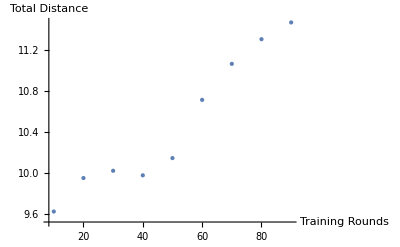

```mathematica
ListPlot[Transpose[{Range[10,90,10],listofSums}],PlotStyle->PointSize[Medium],PlotRange->All,AxesLabel->{"Training Rounds","Total Distance"}]
```

The line graph above shows that the weights of the neural networks do not converge but instead diverge as the euclidean distance between them increases as we train the 2 neural networks for more rounds.

## Conclusion

This project set out to evaluate whether weights of neural networks are computationally irreducible or not as computational irreducibility is characteristic of agents who are able to exercise free will. We were able to reasonably ascertain that neural networks trained to model the same function can take various paths to do so since both of our neural networks ended up with different weights. This leads us to the conclusion that neural networks do have limited forms of free will and agency in the form of their weight trajectories,  even if they are being trained to model a predefined function.

## Limitations and future work

Limitations-

There are various limitations to the experiment we carried out above .
    1) We intentionally chose a simple mathematical function to model. Choosing a simple function inadvertently simplified the loss landscape of the 2 neural networks
    2)We have only compared 2 seeds. Using more seeds would have helped us get a better idea of the variance in the weights.
    3)Comparing weights using the hungarian algorithm only allows us to know whether the weights of the neural networks with random seeds converge or not. Comparing weights does not allow us to verify whether the weights have further diverged independently or are just reflecting the noise from the random initialisation.
    
    
Future work-
-Repeat the experiment for 30 Seeds
-Choose a more complex function to model or more chaotic/irreducible datasets (Rule 110 cellular automata etc)
-Use dropout layers to introduce stochasticity
-Try Monte Carlo Dropout and generate multiple predictions from the same network with different dropout masks

## Acknowledgements

I would like to sincerely thank my mentor, Dr.Lyman Hurd, for his consistent guidance throughout this project. I’m also grateful to the WSRP directors(Rory Foulger, Program Director,Eryn Gillam, Academic Director,Megan Davis, Academic Director) for organizing this opportunity, and to Stephen Wolfram for helping brainstorm and shape the initial idea that inspired this work.I would also like to thank the Notebook assistant for helping me debug my code.

## References

1)Wolfram, S. (2024, August 22). What’s really going on in machine learning? Some minimal models. Stephen Wolfram Writings. https://writings.stephenwolfram.com/2024/08/whats-really-going-on-in-machine-learning-some-minimal-models/ 

2)Kuhn, H. W. (n.d.). Hungarian algorithm. Retrieved July 10, 2025, from https://www.hungarianalgorithm.com/hungarianalgorithm.php
3)Rowland, T. (2025, June 27). Computational irreducibility. In MathWorld–A Wolfram Web Resource. Retrieved July 10, 2025, from https://mathworld.wolfram.com/ComputationalIrreducibility.html